# Cosmology PSET 6:

## Problem 1: Dark Matter and Baryon Density Growth

```mathematica
vMap=ResourceFunction["ViridisColor"];
```

```mathematica
ode=D[ϵ[t],{t,2}]+(4/(3t)) D[ϵ[t],t]==0;
ϵSol = DSolveValue[ode,ϵ[t],t]
```

-(3 C[1])/t^(1/3)+C[2]

```mathematica
params={Ωd ->5/6,Ωb->1/6};
```

```mathematica
odeD = D[Subscript[δ, d][t],{t,2}]+4/(3 t)D[Subscript[δ, d][t],t] -2/(3 t^2)(Ωd Subscript[δ, d][t]+Ωb Subscript[δ, b][t])==0
```

-(2 (Ωb δ_b[t]+Ωd δ_d[t]))/(3 t^2)+(4 δ_d'[t])/(3 t)+δ_d''[t]==0

```mathematica
odeD/.params
```

-(2 (δ_b[t]/6+(5 δ_d[t])/6))/(3 t^2)+(4 δ_d'[t])/(3 t)+δ_d''[t]==0

```mathematica
odeB = D[Subscript[δ, b][t],{t,2}]+4/(3 t)D[Subscript[δ, b][t],t] -2/(3 t^2)(Ωd Subscript[δ, d][t]+Ωb Subscript[δ, b][t])==0
```

-(2 (Ωb δ_b[t]+Ωd δ_d[t]))/(3 t^2)+(4 δ_b'[t])/(3 t)+δ_b''[t]==0

```mathematica
odeB/.params
```

-(2 (δ_b[t]/6+(5 δ_d[t])/6))/(3 t^2)+(4 δ_b'[t])/(3 t)+δ_b''[t]==0

```mathematica
sysSolution = NDSolveValue[{odeD,odeB, Subscript[δ, d][1]==1*^-3, Subscript[δ, b][1]==1*^-4, Subscript[δ, d]'[1]==0, Subscript[δ, b]'[1]==0}/.params, {Subscript[δ, d],Subscript[δ, b]},{t,1,500}]
```

{InterpolatingFunction[…],InterpolatingFunction[…]}

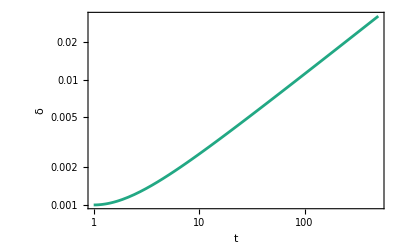

```mathematica
δDPlot = Plot[sysSolution[[1]][t],{t,1,500},  ScalingFunctions->{"Log","Log"}, PlotStyle->vMap[0.6],Frame->True,FrameLabel->{"t", "δ"}]
```

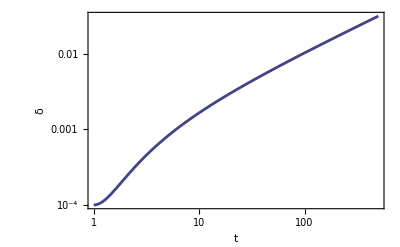

```mathematica
δBPlot =Plot[sysSolution[[2]][t],{t,1,500},  ScalingFunctions->{"Log","Log"}, PlotStyle->vMap[0.2],Frame->True,FrameLabel->{"t", "δ"}]
```

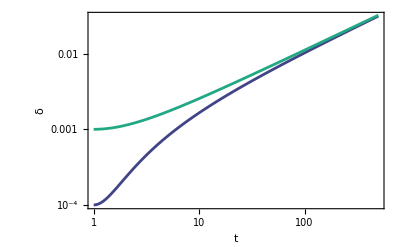

```mathematica
Show[δBPlot ,δDPlot]
```

```mathematica
ratio = (sysSolution[[1]][t])/(sysSolution[[2]][t]);
```

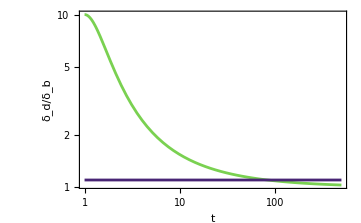

```mathematica
ratioPlot = Plot[{ratio, 1.1},{t,1,500},ScalingFunctions->{"Log","Log"}, PlotStyle->{vMap[0.8],vMap[0.1]} , PlotRange->All,Frame->True, FrameLabel->{"t", "δ_d/δ_b"}]
```

```mathematica
tPerturbation = (t/.FindRoot[ratio==1.1, {t,1,500}]) × 380000
```

3.17432×10^7

## Problem 2: Matter Growth with Dark Energy

```mathematica
ode = a^2(1-ΩM0 + ΩM0/(a^3))f''[a] + (3 a/2)(2-2 ΩM0 + ΩM0/(a^3))f'[a]  - (3/2)( ΩM0/(a^3))f[a]==0
```

-(3 ΩM0 f[a])/(2 a^3)+3/2 a (2-2 ΩM0+ΩM0/a^3) f'[a]+a^2 (1-ΩM0+ΩM0/a^3) f''[a]==0

```mathematica
params2 = {ΩM0->0.3};
ai=1/3600;
```

```mathematica
sol = NDSolveValue[{ode/.params2, f[ai]==2*^-3, f'[ai]==f[ai]/ai},f,{a, ai, 5}]
```

InterpolatingFunction[…]

```mathematica
data = Table[{a,sol[a]},{a,ai,0.5, 0.001}];
model = NonlinearModelFit[data, x0+α a,{x0,α}, a]["BestFit"]
```

0.034241+6.922 a

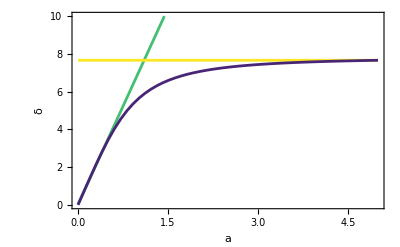

```mathematica
Plot[{model,sol[5],sol[a]},{a,ai,5}, Frame->True, PlotStyle->{vMap[0.7],vMap[1],vMap[0.1]}, PlotRange->{{0,5},{0,10}}, FrameLabel->{"a", "δ"}]
```

## Problem 3: Scalar Field (Inflaton) in Expanding Universe

```mathematica
odeInflaton = D[ϕ[t],{t,2}]+3H D[ϕ[t],t]+m^2 ϕ[t]==0;
```

```mathematica
solInflaton=DSolveValue[{odeInflaton}, ϕ[t], t,Assumptions->{H>0,m>0}]
```

ⅇ^(1/2 (-3 H-√(9 H^2-4 m^2)) t) C[1]+ⅇ^(1/2 (-3 H+√(9 H^2-4 m^2)) t) C[2]